```mathematica
2-2
```

0

# Wigner's Semicircular Law

Nicholas Wheeler
19 July 2011

```mathematica
Hyperlink["Wigner's Semicircular Law","http://mathworld.wolfram.com/WignersSemicircleLaw.html"]
```

Google provides links to many analytical approaches to this subject. Good reviews/discussions can be found in various course notes:

```mathematica
Hyperlink["Analytical Survey","http://www.physik.uni-bielefeld.de/bibos/old-bibos-site/01-03-035.pdf"]
```

```mathematica
Hyperlink["Useful Course Notes","http://www.math.wisc.edu/~valko/courses/833/lec_4_5.pdf"]
```

### Construction of normally distributed symmetric matrices

This is the resource I will use to randomize individual matrix elements:

```mathematica
?NormalDistribution
```

NormalDistribution[μ,σ] represents a normal (Gaussian) distribution with mean μ and standard deviation σ.
NormalDistribution[] represents a normal distribution with zero mean and unit standard deviation.

REMARK: standard deviation =√variance, and has the same units as the random variable.

```mathematica
?PDF
```

PDF[dist,x] gives the probability density function for the symbolic distribution dist evaluated at x.
PDF[dist] gives the PDF as a pure function.

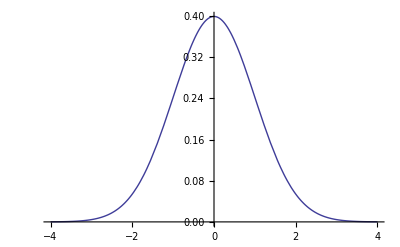

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-4,4}]
```

and this is the construction I will use to create populations of randomized real symmetric matrices:

```mathematica
𝕊=(𝔾+Transpose[𝔾])/2/.𝔾->RandomReal[NormalDistribution[0,1],{4,4}];
𝕊//MatrixForm
```

(2.95239 | -0.940332 | 0.234887 | 1.69491
-0.940332 | -0.907166 | 1.78432 | -0.735883
0.234887 | 1.78432 | -1.95076 | 0.105781
1.69491 | -0.735883 | 0.105781 | 0.957072)

I produce numerical evidence that the individual elements of matrices constructed in this way (I look specifically to a typical 200 × 200 matrix; i.e., to a list of 40,000 matrix elements) are in fact normally distributed

```mathematica
ListOfMatrixElements=Flatten[(𝔾+Transpose[𝔾])/2/.𝔾->RandomReal[NormalDistribution[0,1],{200,200}]];
```

```mathematica
Length[ListOfMatrixElements]
Min[ListOfMatrixElements]
Max[ListOfMatrixElements]
```

40000

-2.99127

2.83924

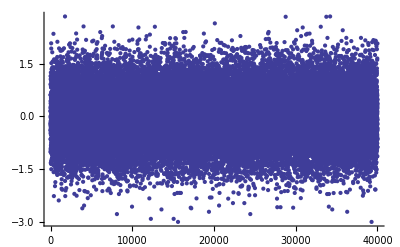

```mathematica
ListPlot[ListOfMatrixElements]
```

All of those numbers fall within the interval [-3, +3]. I partition the interval into 120 bins, each of width

```mathematica
BinWidth=0.05
```

0.05

The bins have endpoints at

```mathematica
BinBoundaries=Table[-3+.05j,{j,0,120}];
```

and midpoints at

```mathematica
BinCenters=Table[-2.975+.05k,{k,0,119}];
```

We distribute the 40,000 matrix elements into their respective bins

```mathematica
?BinCounts
```

BinCounts[{x_1,x_2,…}] counts the number of elements x_i whose values lie in successive integer bins.
BinCounts[{x_1,x_2,…},dx] counts the number of elements x_i whose values lie in successive bins of width dx.
BinCounts[{x_1,x_2,…},{x_min,x_max,dx}] counts the number of x_i in successive bins of width dx from x_min to x_max. 
BinCounts[{x_1,x_2,…},{{b_1,b_2,…}}] counts the number of x_i in the intervals [b_1,b_2), [b_2,b_3), …. 
BinCounts[{{x_1,y_1,…},{x_2,y_2,…},…},xbins,ybins,…] gives an array of counts where the first index corresponds to x bins, the second to y, and so on.

```mathematica
MatrixElementBinCounts=BinCounts[ListOfMatrixElements,{-3,3,.05}];
Length[MatrixElementBinCounts]
```

120

and verify that every matrix element has found a home:

```mathematica
Total[MatrixElementBinCounts]
```

40000

On this evidence, the probability that a matrix element will be found in the k^th bin is

```mathematica
Prob[k_]:=MatrixElementBinCounts⟦k⟧/40000
```

```mathematica
Sum[Prob[k],{k,1,120}]
```

1

and the probability density at the centerpoint of the k^th bin is

```mathematica
ProbDensity[k_]:=Prob[k]/BinWidth
```

We are led thus to the following figure

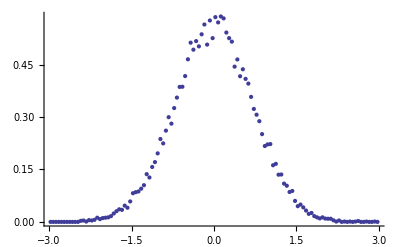

```mathematica
ListPlot[Table[{-3.025+.05k,ProbDensity[k]},{k,1,120}]]
```

and look for the normal distribution function that best conforms to that data:

```mathematica
FindFit[Table[{-3.025+.05k,ProbDensity[k]},{k,1,120}],PDF[NormalDistribution[m,σ],x],{m,σ},x]
```

{m→-0.00135141,σ→0.706164}

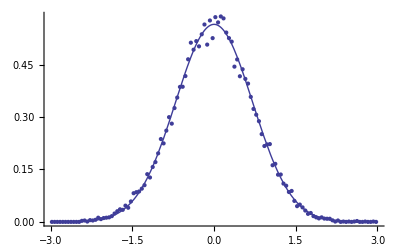

```mathematica
Show[{ListPlot[Table[{-3.025+.05k,ProbDensity[k]},{k,1,120}]],Plot[PDF[NormalDistribution[0.0014,0.7062],x],{x,-3,3}]}]
```

This, I now argue, conforms well to our theoretical expectation. We are reminded

```mathematica
Hyperlink["Sums of Normally Distributed Numbers","http://en.wikipedia.org/wiki/Sum_of_normally_distributed_random_variables"]
```

that if X and Y are independent random variable drawn from normal distributions with standard deviations σ_1 and σ_2 then we expect sums X + Y to be normally distributed with σ=√(σ_1^2+σ_2^2), and therefore expect the averaged sums (X+Y)/2to be normally distributed with

σ=(√(σ_1^2+σ_2^2))/2

Which in the present instance becomes

σ=(√(1+1))/2=1/(√2)=0.707107

—in good agreement with the observed σ → 0.706164. We conclude that the procedure described above does in fact produce symmetric matrices with normally (and identically) distributed matrix elements…the statistical independence of which is compromised only by the symmetry constraint.

### Eigenvalues of symmetric matrices with normally distributed random elements

#### Large population of small matrices

We look first to the eigenvalues generated collectively by a population of 10,000 10 × 10 normally distributed symmetric matrices: at 10 eigenvalues/matrix, this will be a 100,000-element set of eigenvalues.

```mathematica
GaussianEigenvalues10=Flatten[Table[Chop[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[NormalDistribution[0,1],{10,10}]]],{k,1,10000}]];
```

Those eigenvalues are found all to fall within the interval [- 6.60, + 6.60]:

```mathematica
Max[GaussianEigenvalues10]
Min[GaussianEigenvalues10]
```

6.5928

-6.27345

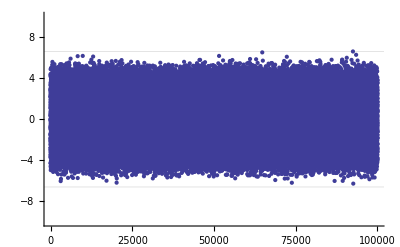

```mathematica
ListPlot[GaussianEigenvalues10, PlotRange->{-10,10}, GridLines->{{},{-6.6,6.6}}]
```

Partitioning the interval into bins of width 0.05—of which there will be a total of

```mathematica
(6.6+6.6)/(.05)
```

264.

we distribute the eigenvalues into their respective bins

```mathematica
GaussianEigenvalueCounts10=BinCounts[GaussianEigenvalues10,{-6.6,6.6,.05}];
```

```mathematica
Total[GaussianEigenvalueCounts10]
```

100000

and plot the result:

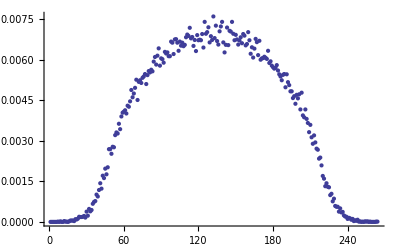

```mathematica
ListPlot[GaussianEigenvalueCounts10/100000]
```

The distribution evidently speaks of a well-defined curve that is, however,  neither Gaussian nor semicircular.

#### Smaller population of larger matrices

We look now to a 1000-member population of 100 × 100 matrices, which will again generate a set of 100,000 eigenvalues.

```mathematica
GaussianEigenvalues100=Flatten[Table[Chop[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[NormalDistribution[0,1],{100,100}]]],{k,1,1000}]];
```

```mathematica
Max[GaussianEigenvalues100]
Min[GaussianEigenvalues100]
```

15.1587

-15.1399

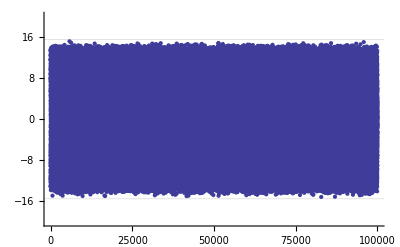

```mathematica
ListPlot[GaussianEigenvalues100, PlotRange->{-20,20},GridLines->{{},{-15.5,15.5}}]
```

Partitioning the expanded interval into bins of width 0.10—of which there will be now a total of

```mathematica
(15.5+15.5)/(.10)
```

310.

—we proceed as before:

```mathematica
GaussianEigenvalueCounts100=BinCounts[GaussianEigenvalues100,{-15.5,15.5,.10}];
```

```mathematica
Total[GaussianEigenvalueCounts100]
```

100000

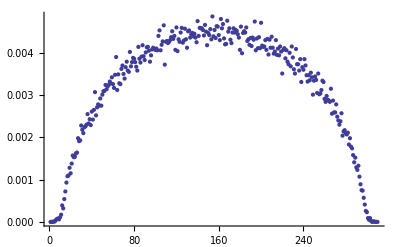

```mathematica
ListPlot[GaussianEigenvalueCounts100/100000]
```

This distribution evidently speaks again of a well-defined curve, but one that is markedly less Gaussian, more nearly semicircular than before.

#### Still smaller population of still larger matrices

We look now to a (to keep the computation time down, only) 50-member population of 1000 × 1000 matrices, which will generate a reduced set of only 50,000 eigenvalues.

REMARK: Execution of the following command takes several minutes.

```mathematica
GaussianEigenvalues1000=Flatten[Table[Chop[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[NormalDistribution[0,1],{1000,1000}]]],{k,1,50}]];
```

```mathematica
Max[GaussianEigenvalues1000]
Min[GaussianEigenvalues1000]
```

45.2567

-45.2105

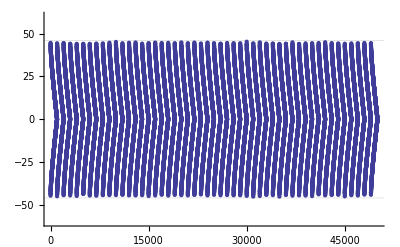

```mathematica
ListPlot[GaussianEigenvalues1000, PlotRange->{-60,60},GridLines->{{},{-46,46}}]
```

REMARK: The herringbone pattern is a reflection simply of the matrix-by-matrix sequence in which Mathematica elects to deploy the elements of the eigenvalue set, and has become visible because of the reduced size of the present population of matrices.

Partitioning the interval into bins of width 0.20—of which there will be a total of

```mathematica
(46+46)/(.2)
```

460.

—we distribute the eigenvalues into their respective bins

```mathematica
GaussianEigenvalueCounts1000=BinCounts[GaussianEigenvalues1000,{-46,46,.2}];
```

```mathematica
Total[GaussianEigenvalueCounts1000]
```

50000

When we plot that data

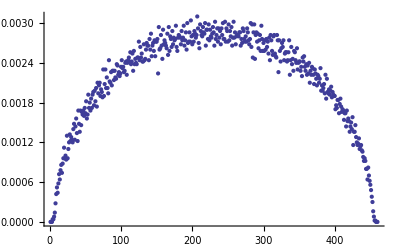

```mathematica
ListPlot[GaussianEigenvalueCounts1000/50000]
```

we see that the hat as pretty much lost its brims. The scatter is so plausibly semicircular that it becomes worth while to make the adjustments required to display density vs. eigenvalue.

```mathematica
BinProb1000[k_]:=(GaussianEigenvalueCounts1000/50000)⟦k⟧
```

```mathematica
Sum[BinProb1000[k],{k,1,460}]
```

1

```mathematica
BinWidth=0.2;
```

```mathematica
EigenvalueDensity1000[k_]:=BinProb1000[k]/0.2
```

```mathematica
EigenvalueDistribution1000=Table[{-46.1+0.2k,EigenvalueDensity1000[k]},{k,1,460}];
```

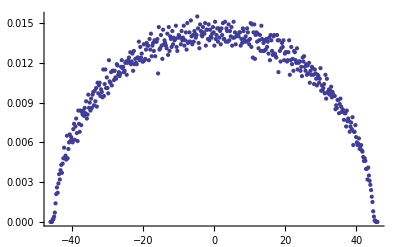

```mathematica
ListPlot[EigenvalueDistribution1000]
```

We undertake to fit this eigenvalue distribution data to an analytic distribution of the centered semicircular form

```mathematica
?Which
```

Which[test_1,value_1,test_2,value_2,…] evaluates each of the test_i in turn, returning the value of the value_i corresponding to the first one that yields True.

```mathematica
Semicircle[r_,x_]:=Piecewise[{{2/(π r^2)√(r^2-x^2),x^2<r^2},{0,x^2>r^2}}]
```

This is a  real-valued non-negative function that satisfies the normalization requirement

```mathematica
Assuming[r∈Reals && r>0,Integrate[Semicircle[r,x],{x,-r,r}]]
```

1

and its form

```mathematica
Manipulate[Plot[Semicircle[R,x],{x,-R,R}],{R,.5,4}]
```

is "semicircular" when the axes are appropriately scaled (which Mathematica manages to do pretty well by itself).

```mathematica
EigenvalueDensity1000[k_]
```

```mathematica
FindFit[EigenvalueDistribution1000,Semicircle[r,x],{r},x]
```

{r→44.7472}

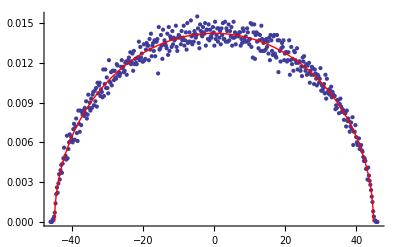

```mathematica
Show[{ListPlot[EigenvalueDistribution1000],Plot[Semicircle[44.7472,x], {x, -44.7472, 44.7472},PlotStyle->{Red,Thick}]}]
```

The radius of the Wigner semicircle can be read as the expected (absolute) value of the largest eigenvalue. In the present instance (1000 × 1000 matrix with normally distributed matrix elements, standard deviation σ=1/√2 = 0.707107) we found

Wigner radius = largest eigenvalue=44.7472

in which connection it is interesting to notice that

```mathematica
N[√(2*1000)]
```

44.7214

### Conclusions drawn from numerical data now in hand

Let the elements of the N-dimensional square matrix 𝕄 be normally distributed with σ_M = 1. Then

• The elements of the N-dimensional symmetric matrix 𝕊=(𝕄+𝕄^transpose)/2 (𝕊  is simply the symmetric part of 𝕄) are normally distributed with σ_S=1/√2. More generally, we have

σ_S=(√(σ_M^2+σ_M^2))/2=σ_M/(√2)

• The eigenvalues of 𝕊 can be expected to conform well to Wigner's Semicircular Law if N > about 1000, but for N ≪ 1000 they conform to N-dependent "Sombrero Laws" for which we possess as yet no analytic description.

• The spectrum of 𝕊 is—for N sufficiently large—bounded (exactly? in good approximation?) by ±√(2N).

### Effect of adjusting the value of σ

I look specifically the consequences of the adjustment σ = 1 → 2.

REMARK: I wish I had assigned a new name to this list. But it took so long to generate (on my home office IMac) that I refrain from that adjustment.

```mathematica
GaussianEigenvalues1000=Flatten[Table[Chop[Eigenvalues[(𝕄+Transpose[𝕄])/2/.𝕄->RandomReal[NormalDistribution[0,2],{1000,1000}]]],{k,1,50}]];
```

```mathematica
Max[GaussianEigenvalues1000]
Min[GaussianEigenvalues1000]
```

90.2389

-90.1749

I partition that iterval into bins of width 0.04, of which there will be a total of

```mathematica
(90.4+90.4)/0.4
```

452.

```mathematica
NewGaussianEigenvalueCounts1000=BinCounts[GaussianEigenvalues1000,{-90.4,90.4,.4}];
```

```mathematica
Total[NewGaussianEigenvalueCounts1000]
```

50000

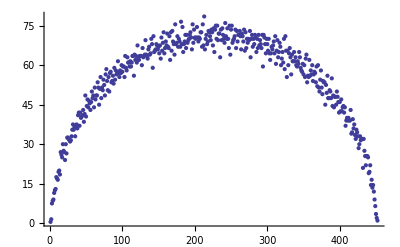

```mathematica
ListPlot[NewGaussianEigenvalueCounts1000/2]
```

It appears on this evidence that the adjustment σ = 1 → 2 has not increased the noise level of the statistics, has not brought about violation of the Semicircular Law; its only effect has been to increase the value of the greatest eigenvalue (radius of the Wigner semicircle), by a factor of about

```mathematica
90.24/45.26
```

1.99381

It appears plausible on this basis to speculate that the spectrum is bounded by ±σ √(2N).

```mathematica
Manipulate[Plot[(1-x^2)^p,{x,-1,1},AspectRatio->Automatic],{p,.5,10}]
```

-Graphics-